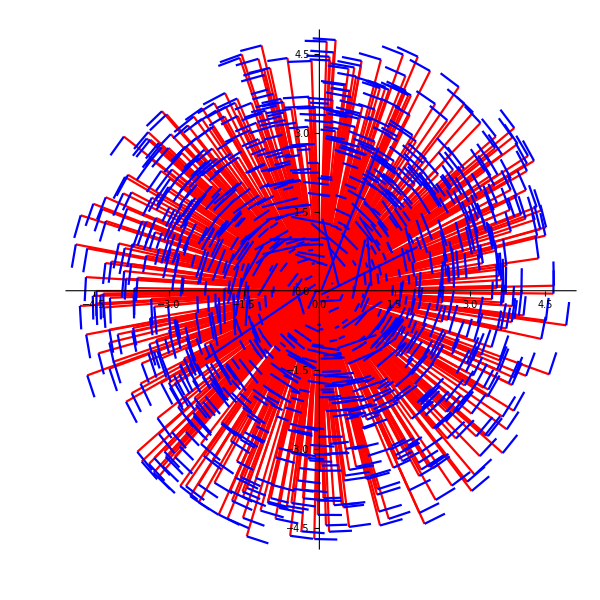

```mathematica
l1=ListPlot[{{0,0},#}&/@clouds⟦All,;;2⟧,Joined->True,PlotStyle->Red];
l2=ListPlot[Table[{clouds⟦i⟧⟦;;2⟧,clouds⟦i⟧⟦;;2⟧+vels⟦i⟧},{i,Length@clouds}],Joined->True,PlotStyle->Blue];
Show[l1,l2,AspectRatio->1]
```

```mathematica
minmass=0.1;
maxmass=10;
α=2.35;
((maxmass^(α+1)-minmass^(α+1))RandomReal[nstars]+minmass^(α+1))^(1/(α+1))
```

17.967

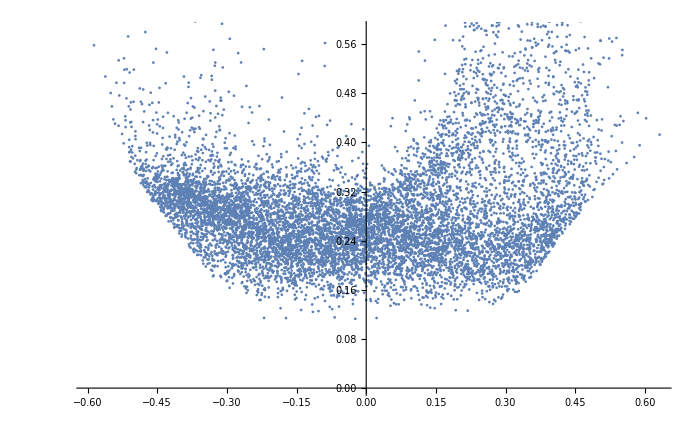

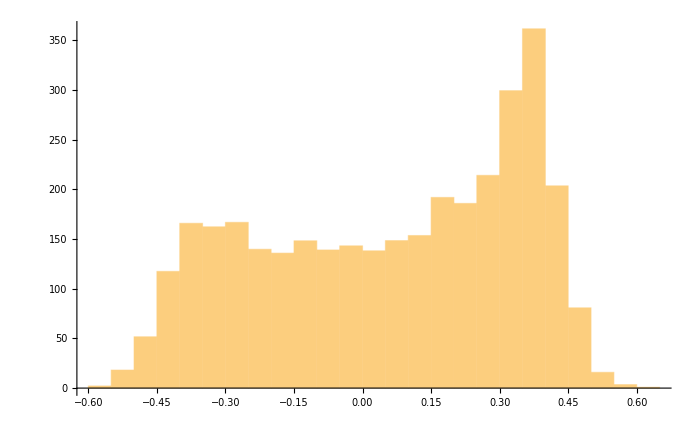

```mathematica
boxsize=5;
nstars=10;
nclouds=10000;
stars={{0,0,0}}~Join~RandomPoint[Ball[{0,0,0},2*boxsize],nstars];
(*stars={{0,0,0}};*)
clouds=1/5 RandomVariate[GammaDistribution[1/0.2^2,1],nclouds]*Normalize/@RandomPoint[Ball[{0,0,0},2*boxsize],nclouds];
vels=1/(Norm/@clouds)^(3/2)(RotationTransform[90°][#⟦;;2⟧]&/@clouds);
losvel={1,0}.#&/@vels;
lums={0.00001}~Join~(10^RandomReal[{-1,1},Length@stars]);
intensities=Total[Table[lums⟦s⟧/Norm[clouds⟦c⟧-stars⟦s⟧]^2,{c,Length@clouds},{s,Length@stars}],{2}];
ListPlot[{losvel,intensities}ᵀ]
vec={losvel,intensities}ᵀ;
vec=Sort[vec,#1⟦1⟧<#2⟦1⟧&];
Histogram[WeightedData[vec⟦All,1⟧,vec⟦All,2⟧]]
(*vec⟦All,2⟧=Accumulate[vec⟦All,2⟧];
vec⟦All,2⟧=Rescale[vec⟦All,2⟧,{0,Max[vec⟦All,2⟧]}];
intf=Interpolation[vec,InterpolationOrder->2];*)
(*line=D[intf[x],x];
Plot[line,{x,Min@losvel,Max@losvel}]*)
```

```mathematica
ListPointPlot3D[{stars,clouds},PlotStyle->{Directive[PointSize@0.05,Orange],Directive[PointSize@0.005,Blue]},BoxRatios->1]
```

-Graphics3D-

```mathematica
boxsize=5;
lights=RandomPoint[Ball[{0,0,0},10],10];
lights={"Point",Directive[{Red,Opacity[1]}],#,{0,0,1}}&/@lights;
Append[lights,{"Point",Red,{0,0,0},{0,0,1}}];
images=Table[Dynamic[Graphics3D[Join[{}, Sphere[#]&/@RandomReal[{-boxsize,boxsize},{1,3}]],Lighting->lights,ViewPoint->{0,0,∞},Boxed->False,SphericalRegion->True,Boxed->True,ImageSize->200,PlotRange->1.2*boxsize*{{-1,1},{-1,1},{-1,1}}(*,Background->Black*)]],{i,10}]
```

{,,,,,,,,,}

```mathematica
Total[List@@#&/@DeleteCases[Reap[ImageScan[Sow[RGBColor@@#]&,Rasterize[Dynamic[image]]]]⟦-1,1⟧,x_/;x==RGBColor[1.,1.,1.]],{1}]
```

{0.,0.,182.137}

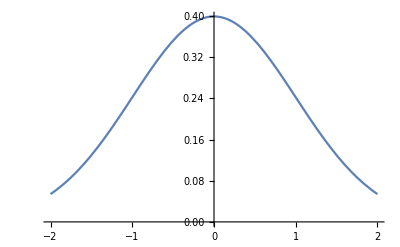

```mathematica
func=PDF[NormalDistribution[]];
Plot[func[x],{x,-2,2}]
```